# The Sphere

## Computing Parametrization and Stereographic Projection

```mathematica
n={0,0,2R}; (* North pole of sphere with centre at (0,0,R) *)
xy={x,y,0}; (* x,y coordinates in space *)
l=xy+λ(n-xy); (* line joining (x,y) with north pole *)
d=l-{0,0,R}; (* Distance of line points to centre of sphere *)
sol=Simplify[Solve[Dot[d,d]==R^2,λ]];
p=Simplify[l/.sol][[2]]; (* Intersection of line with sphere *)
z=Simplify[({x1,x2,x3}+λ({x1,x2,x3}-n))/.Solve[x3+λ(x3-2R)==0,λ]][[1]][[1;;2]];
Print["Parametrization p = ",p];
Print["Stereographic projection z = ",z];

(* Verifying p is inverse of z *)
Print["z(p(x,y)) = ",Simplify[z/.{x1->p[[1]],x2->p[[2]],x3->p[[3]]}]]
Print["p(z(x1,x2,x3)) = ",Simplify[p/.{x->z[[1]],y->z[[2]]},x1^2+x2^2+(x3-R)^2== R^2]]
```

Parametrization p = {(4 R^2 x)/(4 R^2+x^2+y^2),(4 R^2 y)/(4 R^2+x^2+y^2),(2 R (x^2+y^2))/(4 R^2+x^2+y^2)}

Stereographic projection z = {-(2 R x1)/(-2 R+x3),-(2 R x2)/(-2 R+x3)}

z(p(x,y)) = {x,y}

p(z(x1,x2,x3)) = {x1,x2,x3}

## Plotting

```mathematica
sz=15;
rVal=5;
sG=ParametricPlot3D[p/.R->rVal,{u,-sz,sz},{v,-sz,sz},PlotRange->All,PlotStyle->
Directive[Orange,Opacity[1]],PlotPoints->100,Mesh->20,Boxed->False,Axes->False];
s2G=ContourPlot3D[x0^2+x1^2+(x3-rVal)^2==.98rVal^2,{x0,-rVal,rVal},{x1,-rVal,rVal},{x3,0,2rVal},Mesh->None,
ContourStyle->Directive[Opacity[.3],Specularity[1]] ];

aG=ContourPlot3D[x0^2+x1^2+(x3-rVal)^2==.98rVal^2,{x0,-rVal,rVal},{x1,-rVal,rVal},{x3,0,2rVal},Mesh->None,
ContourStyle->Directive[Opacity[1],Specularity[1]], RegionFunction->Function[{x,y,z},1.6rVal<z<1.8rVal]];

pG=ParametricPlot3D[{x,y,0},{x,-sz,sz},{y,-sz,sz},Mesh->20,PlotStyle->Directive[Opacity[1]]];
lG=Graphics3D[{PointSize[.01],Point[{{0,0,.98*2rVal},{5,-5,0},p/.{x->5,y->-5,R->rVal}}],
{Thick,Line[{{0,0,.98*2rVal},{5,-5,0}}]}}];
Show[sG,s2G,pG,aG,lG,Boxed->False]
```

-Graphics3D-

ρ(h)=-(2 R √(-(h-R)^2+R^2))/(h-2 R)

(2 R ρ^2)/(4 R^2+ρ^2)

h(ρ) = (2 R ρ^2)/(4 R^2+ρ^2)

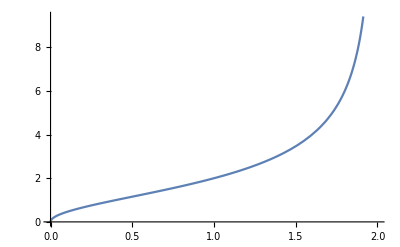

(2 R ρ^2)/(4 R^2+ρ^2)

```mathematica
ρ[h_]:=(z/.{x1->Sqrt[R^2-(h-R)^2],x2->0,x3->h})[[1]]
Print["ρ(h)=",ρ[h]]
hρ=Simplify[h/.Solve[ρ[h]==ρ,h]][[1]]
h[ρ_]:=Evaluate[hρ]
Print["h(ρ) = ", h[ρ]]
Plot[ρ[h]/.R->1,{h,0,2}]
```

```mathematica
(* Metric tensor and volume form in x,y coordinates *)
px=Simplify[D[p,x]];
py=Simplify[D[p,y]];
xxC=Simplify[Dot[px,px]];
xyC=Simplify[Dot[px,py]];
yyC=Simplify[Dot[py,py]];
gxy={{xxC,xyC},{xyC,yyC}};
Print["Metric tensor in x,y coordinates = ",MatrixForm[gxy]]
μxy=Simplify[Sqrt[Det[gxy]],R>0 && x∈Reals && y∈Reals];
Print["Volume form in x,y coordinates = ", μxy];

(* Metric tensor and volume form in u,v coordinates *)
sbs={x->Exp[v]Cos[u],y->Exp[v]Sin[u]};
q={x,y}/.sbs;
qu=D[q,u];
qv=D[q,v];
uuC = Simplify[Dot[qu,(gxy/.sbs).qu]];
uvC=Simplify[Dot[qu,(gxy/.sbs).qv]];
vvC = Simplify[Dot[qv,(gxy/.sbs).qv]];
guv = {{uuC,uvC},{uvC,vvC}};
μuv=Simplify[Sqrt[Det[guv]],R>0&& v∈Reals];
Print["Metric tensor in u,v coordinates = ", MatrixForm[guv]]
Print["Volume form in u,v coordinates = ", μuv]
```

Metric tensor in x,y coordinates = ((16 R^4)/((4 R^2+x^2+y^2)^2) | 0
0 | (16 R^4)/((4 R^2+x^2+y^2)^2))

Volume form in x,y coordinates = (16 R^4)/((4 R^2+x^2+y^2)^2)

Metric tensor in u,v coordinates = ((16 ⅇ^(2 v) R^4)/((ⅇ^(2 v)+4 R^2)^2) | 0
0 | (16 ⅇ^(2 v) R^4)/((ⅇ^(2 v)+4 R^2)^2))

Volume form in u,v coordinates = (16 ⅇ^(2 v) R^4)/((ⅇ^(2 v)+4 R^2)^2)

```mathematica
(* Computing σ and J *)
σPrim=Simplify[Integrate[μuv,v],R>0&& v∈Reals]
σ=Simplify[(σPrim/.v->Log[ρ[h2]])-(σPrim/.v->Log[ρ[h1]])]
j=Simplify[(1/2)Log[ρ[h2]^2/ρ[h1]^2],R>0&&h1∈Reals && h2∈Reals]
Simplify[j/.{h1->(R-w/2),h2->(R+w/2)}]
Simplify[σ/.{h1->(R-w/2),h2->(R+w/2)}]
Limit[σ/.{h1->h[r1],h2->h[r2]},R->Infinity]
Limit[j/.{h1->h[r1],h2->h[r2]},R->Infinity]
```

-(8 R^4)/(ⅇ^(2 v)+4 R^2)

(-h1+h2) R

1/2 Log[(h2 (h1-2 R))/(h1 (h2-2 R))]

1/2 Log[(2 R+w)^2/(-2 R+w)^2]

R w

1/16 (-8 r1^2+8 r2^2)

1/2 Log[r2^2/r1^2]

```mathematica
FullSimplify[Solve[r==2R Sqrt[R^2-h^2]/(2R-h),h]]
```

```mathematica
h[x]
```

x^(-1)[x]

```mathematica
f1 = 2R Sqrt[R^2-h^2]/(2R-h)
hκ=Simplify[Solve[R Sqrt[R^2-h^2]κ==h,h][[1]],R>0 ]
```

```mathematica
ρ=Simplify[(2R Sqrt[R^2-h^2]/(2 R-h))/.hκ ,R>0&& κ>0]
```

```mathematica
r = Sqrt[R^2-h^2];
α={r Cos[s/r],r Sin[s/r],h};
αd=D[α,s];
αdd=D[αd,s];
n=Simplify[α/Sqrt[Dot[α,α]],R>0];
κ=Simplify[Dot[Cross[n,αd],αdd]]
```

```mathematica
Plot[κ/.R->1,{h,-1,1}]
```

```mathematica
Simplify[(2R Sqrt[R^2-h^2]/(2 R-h))/.Solve[κ==x,h],R>0 && x∈Reals]
```

```mathematica
Plot[Tan[θ],{θ,-Pi/2,Pi/2}]
```

```mathematica
kk=Simplify[2R ^2Cos[ArcTan[κ R]]/(2R-R Sin[ArcTan[κ R]])]
Limit[kk,R->Infinity]
```

## Example of channel of constant width

```mathematica
α={Cos[2u],Sin[2u],u};
α=Simplify[α/Sqrt[Dot[α,α]]];
αt=Simplify[D[α,u]];
αt=Simplify[αt/Sqrt[Dot[αt,αt]]];
αn=Simplify[Cross[α,αt]];

β=Cos[v]α+Sin[v]αn;
αG=ParametricPlot3D[α,{u,-Pi,Pi}];
wd =.2;
βG=ParametricPlot3D[β,{u,-Pi,Pi},{v,-wd/2,wd/2},Mesh->None,PlotPoints->100];
sG=ContourPlot3D[x^2+y^2+z^2==.99,{x,-1,1},{y,-1,1},{z,-1,1},Mesh->None,ContourStyle->Directive[Gray,Opacity[.3],Specularity[1]]];
Show[sG,αG,βG,Boxed->False,Axes->False]
```

-Graphics3D-

```mathematica
sG=ContourPlot3D[x^2+y^2+(z-1)^2==.99,{x,-1,1},{y,-1,1},{z,0,2},Mesh->None,ContourStyle->Directive[Gray,Opacity[.3],Specularity[1]]];
ρ=Sqrt[R-(h-R)^2];
p={ρ Cos[t],ρ Sin[t],h};

pd = Simplify[D[p,t]];
pdd=Simplify[D[pd,t]];
Print["Geodesic curvature = ",FullSimplify[Dot[pdd,Cross[α/R,pd]]/Dot[pd,pd]^(3/2),R>0]]
Show[sG,ParametricPlot3D[α/.{R->1,h->.1},{t,0,2Pi}]]
```

Geodesic curvature = h/(R √(-(h-R)^2+R))

-Graphics3D-

h/(R √(-(h-R)^2+R))